```mathematica
sourceFolder = "source";
sourcePath = FileNameJoin[{NotebookDirectory[], sourceFolder}];
$Path=Once[Append[$Path,sourcePath]];
<<"SeriesGenerator.wl"
```

# Painleve 1

## Expansion at x=∞

### Getting the Coefficients

The Painleve 1 equation has the form

y''[x] == 6 y[x]^2 - x;

We transform it by defining t = (24 x)^(5/4)/30, y[x] = - √(x/6)( 1 + h[t])

h''[t] + 1/t h'[t] + h[t] ( 1 + 1/2 h[t] ) - 4/(25 t^2)( 1 + h[t] ) == 0

Plug in h[t] ~ ∑_(n=1)^∞ a_n/t^(2n), t→∞   and solve for a_n to some order N

```mathematica
orderN = 30;
coeffs = Painleve1PertSol[orderN];
```

```mathematica
coeffs;
```

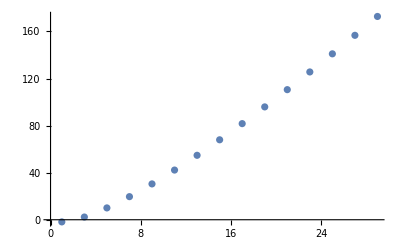

```mathematica
ListPlot[Log@coeffs]
```

### Determining the Growth of the Coefficients

From the Log plot of a_n we see that they grow faster than exponential.
Guessing the growth as

a_n~ c (-1)^(n+1) Γ[2n - 1/2] + ...,    n→∞

We construct new coefficients A_n = a_n/((-1)^(n+1) Γ[2n - 1/2])	and try to find its limit.

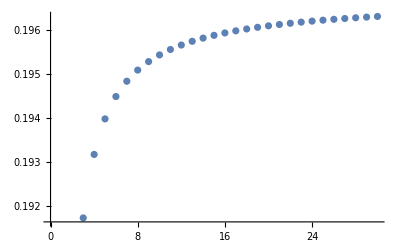

```mathematica
Atable = Table[ coeffs[[i]] / (-1)^(i+1) / Gamma[2i-1/2], {i,1,Length@coeffs}] // N;
ListPlot[Atable]
```

From a Richardson extrapolation we can get a pretty good value for c:

```mathematica
anprefactor = RichardsonExtrapolate[Atable, 6]
Print["The analytic result is ", 1/Pi Sqrt[ 6 / (5 Pi) ] // N]
```

0.196728

The analytic result is 0.196728

#### Higher corrections

a_n~ c (-1)^(n+1) Γ[2n - 1/2] ( 1 - c_2/(2 n - 3/2) + c_3/((2n - 3/2)(2n - 5/2)) - ...)

```mathematica
A2Table = Table[ (Atable[[n]] - anprefactor )(2n - 3/2) , {n,1,Length@Atable}];
```

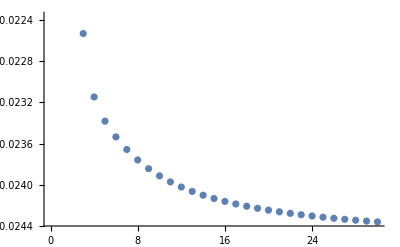

```mathematica
ListPlot[A2Table]
```

```mathematica
c2 = RichardsonExtrapolate[A2Table, 6] / anprefactor
```

-0.125

```mathematica
1/8 // N
```

0.125

### Borel-Pade Transformation

```mathematica
BT = BorelTransform[coeffs, p];
```

```mathematica
BT;
```

```mathematica
BTcoeffs = BorelTransformCoeffs[coeffs];
```

Use Pade approximant for analytic continuation

```mathematica
PBT = PadeApproximant[BT, {p, 0, {orderN-1, orderN}}]
```

((4 p)/25+(2195138856643159463273406280754877180300405583860273950895554651534845843083759531680771139294118520995554682606292969763212467086652549202196791194266244636395890368079452228058364122215925021560145797722019803600655331290119243728760228250105217507008526345215053387273656525506134678839989154025566527569353927101740199433029566556793053749242769891879614628507709461946375751200205059661562005468379804484093918561423021076894220518703918015198328438549522638874125782036030691343349687133425744056255286199127053973774156497130729784097720754670765273058021153980315618007728241888846798640918231232540563745640675173410706336883891819092 p^3)/1974579421753487584223379439989679523197181601082983374947698350230455366229099018801121317818443693332117465453008329515689649610196051857554131890455415821936945859038108228255367462992312136750574374433935727185548668435519825090245878839499164343453694404277045337172233381760891068635241300971510370587282651006945245970298253928329403562493786572783428372778147728546927361589626852796225201075981168830653294169230600861169954687703638091988621281984312643859767062266923812873143975359567464939718944034695210326842837995662319796975340381430326152316297152563011525386688741978731471278897299969833092114486900915091856005481534901875+(48609192331634384174890603058817698366782136428430407182991711904891727046319759414926795695137771972243639705515770474415874196408506422703914981128780175540114362975168233214942029497584987337361986318811238364658671136361744799525492863469063669830282242611047562327038850215325118437995623027432886010058956076872302978717240906419460441127987029785613221452392010848549805752280508509376429120700726683485207343420669410208525378507877312957751718410355379842021512737755507277520882606855061025602014044723989863731978759189202562986343361143152510826815467906813746726280534332077862790150303488330841864386084513445738909359266221085697612 p^5)/14068878379993599037591578509926466602779918907716256546502350745391994484382330508957989389456411314991336941352684347799288753472646869485073189719494837731300739245646521126319493173820223974347842417841792056197034262603078753768001886731431545947107572630473948027352162845046348864026094269422011390434388888424484877538375059239347000382768229331081927156044302565896857451326091326173104557666365827918404720955768031135835927149888421405418926634138227587500840318651832166721150824436918187695497476247203373578755220719094028553449300217691073835253617212011457118380157286598461732862143262285060781315719169020029474039055936175859375+(73569826066386433182491532252032915386455495366513283979134256488702909454646991580077851757533991701726758559300124420203487766551324899519497426314203752895668132252584656637079583103720070785596894558512618678509209840642996593951835068207322608961744330829033989853401624954300553688467692569578480780099294126420097072512886123858707788060592122378855449901179470713850692273538559160885311671763177800503807982571935597025193255455266930736869658618877443265389972820473446748290756754760662390479927219707822166841831144049779575750063302168155484406626382066944014977471193981152088846995205763910517559887348567978987139577207091979444886903 p^7)/11606824663494719206013052270689334947293433098865911650864439364948395449615422669890341246301539334867852976615964586934413221614933667325185381518583241128323109877658379929213581868401684778836969994719478446362553266647539971858601556553431025406363747420141007122565534347163237812821527772273159397108370832950200023969159423872461275315783789198142589903736549616864907397344025344092811260074751808032683894788508625687064639898657947659470614473164037759688193262887761537544949430160457504848785417903942783202473057093252573556595672679595135914084234199909452122663629761443730929611268191385175144585468314441524316082221147345083984375+(3519321112326870212381695558452942260261864394899068832048809285649218932535319669690439284336511685907376624882151795729433409746117947508496471161699233810366960844912334780219697643669159457183161786374654810657559459583795131130544960436442559009112381613970718936491463512941289741357718313604758993373863516853407868495859231834036940859228289413144325090650043868814038655839828180729364505606311452958321796057320803682207167300509077808863370387268344640513495025983782983936511731221967313776897592087264250152060032315622773062249702370334618955763065528090819848059640303670130966767313596534862817967309073733019875067511557097694800021107557 p^9)/461371280373915088439018827759901064154913965679919988121861464756698719122213051128141064540486188560997155820484592330642925559193613276176118915363683834850843617636920602186239879268966969958769557290099268242911492349239713881379411872998883259902958959950605033121979990299738703059655728947858086035057740609770450952774087098930335693802405620626167948673527847270380069044425007427689247587971384369299184817843217871060819435971653419463956925308270500947605682199788521117411739848878185817739220361681725632298304019456789798874677989013906652584848309446400721875879283017388304452047910607560711997272365499050591564268290606967088378906250+(7446693686215348435952312573345355210917666616324917649642385295997413978955136097941246492294736009757517902068058239974498484690197283020775348536028280491354771487018069799754284329824332978792313734427734113019909859360280367491928105563707497274014958042971939245869615856431362365200912998711123946888721937465799906769563531573084461702456623186558247610419389192208174092337985475146624630599527726356639252384440718999023822349679001479115680569291485458581613335883292309080291743904653787172416524230581543563740180170425780039064887035783245590898045137838154249816615735994971028562740077889512044396230390423482521431377881143720101412335336861 p^11)/1176496764953483475519498010787747713595030612483795969710746735129581733761643280376759714578239780830542747342235710443139460175943713854249103234177393778869651224974147535574911692135865773394862371089753134019424305490561270397517500276147152312752545347874042834461048975264333692802122108817038119389397238554914649929573922102272356019196134332596728269117496010539469176063283768940607581349327030141712921285500205571205089561727716219633090159536089777416394489609460728849399936614639373835235011922288400362360675249614813987130428871985461964091363189088321840783492171694340176352722172049279815593044532022579008488884141047766075366210937500+(59503337967378121323995133582615539183053449225205176179622588272242398879561286400770142026605262407516239090928893979401902095048892507471996811389019482427587326137562367909026343171321314326683100629829139640184591063542152852894301573280433782356973370244166179074868900125297562603967936724687450638761009330964926703634574785013309327872897158572295332166125960869169182668176078139543940463777535186763429275479967974502409285149583742729070226802359347580556716634148706205687603940511740776539276843291140878915684171150113509451153354707119655218123569181933885616571563742568733953295331985567267913212611028762482304043033275550987783602668542435269 p^13)/16059180841615049440841147847252756290572167860403814986551692934518790665846430777142770103992973008336908501221517447548853631401631694110500259146521425081570739220897113860597544597654567806839871365375130279365141769946161340926113878769408629069072243998480684690393318512358154906748966785352570329665272306274584971538684036696017659662027233639945340873453820543863754253263823446039293485418313961434381375547077806046949472517583326397991680677667625461733784783169138948794309134789827452850957912739236664946223217157242210924330354102601555809847107531055593126694668143627743407214657648472669482845057862108203465873268525302006928748779296875000+(7779293064137346251322177284076404901923084294520077340840403220686209490856763644420172097493109090350950432215653966851220847674978408849153898735924173665534552058178209033696608749827479150299405915621823308437579601586901961202427171183677313230482641582065486770744305434302885681483279924763427285755100253985308859812945736033417583853608037038229188045289836145843637147533935287625458023955405918502625206492836233880749084579939874808065841741721915252363470676543865970299088620833320319123889505896767266051047783495745677997483161686778153911912834732400883380113828746305496496702239674006272343545818599639257132792604089752945076915069324127776143 p^15)/5054340398811879399907593407282675528952401045350307841749528356623101526527559686556095055051359808427464505964807946661581165240245689441027983347454287804690790692291279139161280777386817099920584514548869128103761137416090957746834948451979055131114255365593251208360397121077008575561616778425697358220543292823027859345880466906559129491843392730429225587403992626528547655603123004222188351437460420897874495428879398778169365234328680852939345927569498192197463514345644178080351758940548372437466664500518682494235432185649892277523615911756293234795629825622407658178455821989981742002827518827335707770431157493876537250292102829426287842807769775390625+(42041814678673744506646191804257974468430355742174306399597591898267089943330980910724210261822975360306964165589771831140355147292442913041372545215698852283583269484521594724361182089725363044764220039195672994302424601616911496738522395812013114099252569924692645580460979154874841755980544971939846614640158935274758649761306936639261214615906862477914821223153152450484036932956771426057827714225656554357605334123679316772904622779491804059669992575059927684574386649277960791083341951036895716934122286509882475300533535080032445118639882563634231640407018869604698464789693244234605567271825303996949397125038505173536068300966926899513426346423591890742244041 p^17)/93404210570043531310292326166583843775040371318073688915531284030394916210229303007556636617349129259739544070229650854306019933639740340870197132260955238630685811993542838491700468766108380006532401828863101487357505819449360899161509847392572938822991439156163282330500138797503118476378678065306887179915640051369554840711871028433212713009265897658332088855225783738247560675545713118026040734564268578192720675525691289420569869530394022162319112741484326591809125745107504410924900505221333922644383959969585252493470786790810009288636422049256298979023239177502093523137863590374862592212252547929163879597567790486838408385398060287797799335087585449218750000+(682808890602936241796609731175693814577685671107820874390291327486460619771967481126884566146789794187814607020024738491402591012987742594198879822087659511776918356387554029113153075139940676504973899907652733888257219157469238668699912950319512949167520586552587475231268397174213033907900088327643986886657901920624127856733668361705032593893115078336340887308361716475370241442762783415185653421697698693799106726950767716762489316759099306313512291724845696060481236968904253520685031651871805390889783852492967409733306299333982824243142852329443060128360278214106223422619354496428546069832344462430788065355706083592535582923716701585214686535007091416592803634907 p^19)/7530714477209759711892318797180822404362629937519691168814709774950590119449737554984253827273773546566500740662265600128422857149704064982659643788539516114599043591979391353393350294267488138026674897452087557418198906693104722494896731446026193192603684781965664637896573690548688927158030919015367778880698479141670359032394601667427774986372062998703024663952578813896209579465873120140849534224244154116788104464258860209533445730888018036836978464782173831464610763199292543130820103233470047513203456772547810982286082185009056998896311527721289105183748658686106290302990251973973296497112861676788837792553903108001346676072718610703697571391436576843261718750000+(70040631146042180484339281933432749972408350788093937370544421476550290489187237109654362150818640821215498316529812753547504374262681589148590619820762401498599229650019464937295329505392639870931731173796651464321120132314670093072611122394348909569671225581513240831637015688971399180367416016709031300595303894722077098268281825298803998541188139898451089958562050670084349880109735527932121196532476465546980176171660379165090513491123681829162975290123798017849665167963730065075770855857086595458109754977397485549683814645340616535017821960589854154362927514715633998021782901630789597298651469679933918076717104209607441443558939280477857991565327319898169462802497 p^21)/5789236754355002778517220075332757223353771764468262586026308139493266154326985745394145129716713413922997444384116680098725071433834999955419601162439753013098014761334157102921138038718131506108006327416292309765240409520324255417951862299132636016814082676136104690382991024609304612752736268993063980014536955840159088506153350031835102020773523430252950210413544963182711114214389961108278079434887693477280855306898998786078836405620163865818427194801296132938419524209456142531817954360730099025775157393896129692632425679725712567901539486935740999610006781364944210670423756204991971682155512414031419053025813014276035257230902431978467508007166868448257446289062500+(225378507917973161040560688663658294612727251531312759386136830892756921944609369397140284917718080376460253425599238888793163188669306211341337890468665171590917707415929680144994169782738707025909901765576996578584796831500951485181018916439415121971347747455593938912518817508570985887449696444087024357305641126416187922598238176728695190240975136542909608371615445609345436939308275974255369910144142467926705525430292476568567787122049501105329634685375544890277160966848377359887876209543941329343587032544429425930638920920419081544811834207194349400650788511239900662522786161558444512723509920262414865144809527051770601367500457854113256503635546647624202320673581489 p^23)/224879685480278774596624459815147991698275400984233844452755258396316205283634912954421459705440334389719989617409687929168253885918746220490521396265437517042118440062491258131247762037317641615039890229415087943769783018700595521568441228864085505719800367064131355528654851355934765846484066626663907490342457751302179704639023463458839074051380421246270154840063924347630645058816747822606001841159637515517487446143543330623684578600534365276680238589170347563919051740402874158791506316056804735490110558322898548949366224181345457082042022736970561495962041196131610672264460574362799255564618571105042677881980469976766880658658165579963582311033948578834533691406250000000+(38901805595438869946395384130456694175086654895245708823136248301150472555703189150948676936215724405981157036850020541292128942575169044198351560194400617537067044684147181300289151767751088910033848633182569468918430367865942455913110510612990749922309848401682155103502195116512343994302546172806341024227729347747541299769748382598636204718570774324250264239931107353367908015075031439509629012901732366537055508316829713884217538547967165861941422550030932440349609385174665279947265776376461227715417522432077283175693099109300350016854861129271700675647436650056959231077765675068358533316104667915749068711410720661937140302394034705871474113932069174662938385221875554011711 p^25)/842455521730494359332604382582498163899664220937186039781134386767199584043817292655501393421505852707488511104221043404646571120123103028512615780759395298219036206084107875774186928532301214900343188771946273209347549633807105972675772953632080325802802125114002090649223236892170616552390934600139663435695432350815790718503941649982675881164983903093839567569589476587311304051592241530437734397444292042507387345115249202348978352582251865917763343814679414561331747582484267317372680536527804740329826679117158689001563217339365418593599927678375966004247796831008046480970735426706636711158952322002266132015369335650462926667498152803938570232710929863458871841430664062500000000+(53746017879755047251741500883468059993598136148759722676801984608193048737707577474389717860689457554774597784491607602992807124685457754167641448646814368947160661338400990577580775551394032268278759404784394349828490226247310595681178369969947081268689040029817284553185361035222967073674802957009031099703878344627019705453942332526931862327874726349769315081167384014441753227251163167522161961036837872537831092736258222028007847624207007868172484586557245537762290312355550853963622567514067593968003573911588185198533722930405223681528426880170071993506959439128917852760065710414403433041414180783004428068896966617925420321154883474112675811342741585132620516783299536050809273 p^27)/55854801090731776023751670565219628266547737848135434437489209842665332422105086503059742383845838034506488286209855177728067665264161730790386426264347908271922100463376352163828593361691570547892753415580037913779742540721411125988403746825806925600725780895058338610043500605950911877423518963989259685786607164859086924636811331393851410921238432775121563329863782297738739458620565613468021790550556562418239780981141022115737264776203298710347709694913245185416294864718706923141808719571793454283867508825467621080803641309599927252755675205076326546081628929895833481688359758790650013949838538948750244552618986953625692038055127530901127206428734649947323203086853027343750000000000+(2723078876379028217660535622657003526715331380584969775887691531659953750415768612270417467802264836293515316619930530262374569583323983820875315256698539984912101518753861788283882977341145859260893325376573442639455278807366627098558813478386187615336851331454654870583236432006140598776982590744454956240500242223138797718004199645394073690332057768792757697400082802667149627779385966061221941061008101059234145458690966710097755009411592762781995684452693370350546641388114172679033710520277619995856732076767616101006415616662177139956583955453563962503677819356589691599361353002480164957385988314679181661129751915908111946490228720827114661101328626085717171795193026782977646493 p^29)/494935598553984348654910636397362817139686899265422321821084942772506695629208960957668272790189509250210271202803994491534821811646322003392590832731305076076198612439362676118370035621655861243827453876945335958214940846948059699730577645484233590739764558486766944905663241480509469136058404153127051104609102377501353582198411519851072224552085001535104963950737404249407163536110011963786081977378542872539402503693999612636671873989134785794469983129925700392994390606812986346728805042872280886570937092092338086799343377160066022045251677511648560227778878573243635573849632307061593179166624831240314667007929356616849882226099602287707210523632398703699891716241836547851562500000000000)/(1+(600387056382614341352722552887116253281321075140037119922521846436400694341727003944862088595851625434634673748745193452146472948142927455759945778637129359245591443802725618712997966920180345897118126415711804570612838024311395694548482696198549204927721466735536798296515163753218289636998261171780436243686135055083218952947852675191938517077196762071977251935529626125953639516260180001798519955213925666464552394644981638395463278847967912603551412473237363478066691402916615145588917672753132431155143287221798323318365290569324403385385750635737175045037854082058939032037526262589215442984740580680112410335426470600410421164223733542 p^2)/78983176870139503368935177599587180927887264043319334997907934009218214649163960752044852712737747733284698618120333180627585984407842074302165275618216632877477834361524329130214698519692485470022974977357429087421946737420793003609835153579966573738147776171081813486889335270435642745409652038860414823491306040277809838811930157133176142499751462911337134911125909141877094463585074111849008043039246753226131766769224034446798187508145523679544851279372505754390682490676952514925759014382698597588757761387808413073713519826492791879013615257213046092651886102520461015467549679149258851155891998793323684579476036603674240219261396075+(14652966479705266292173659647013088088944631540587153385455058025134048362387192467254416914695896936900382115025471373359053250469797129097840029395348642311481091459531429457163593373122351528601215899352268975519311215443450713694053376706138368485908241761954705704404814756555408414175227118420143248426416354205493565065546852902719636124322033925966539980448860236109415330235927449259953684614424339939680212552791151774582349739726284942424836401487381676066427731324172691717353536910869918290110169279606738597755171077066986687387364251779622872889482563609634845942667112766666655462965297682270051965258569821767554979759487312079113 p^4)/562755135199743961503663140397058664111196756308650261860094029815679779375293220358319575578256452599653477654107373911971550138905874779402927588779793509252029569825860845052779726952808958973913696713671682247881370504123150150720075469257261837884302905218957921094086513801853954561043770776880455617375555536979395101535002369573880015310729173243277086241772102635874298053043653046924182306654633116736188838230721245433437085995536856216757065365529103500033612746073286668846032977476727507819899049888134943150208828763761142137972008707642953410144688480458284735206291463938469314485730491402431252628766760801178961562237447034375+(32871925113524362597533106916433974101305479164092916308603636243810142934323381636308423218043204494796579382146993528923641483638588343545655710706923040589773176868155155171376377988503611878341919043516737813932152183870555210880212492223198677131464874720616038009458481230634942482813083176984887445043354762058190531261353642663718176471683637819718988700285389496232097040162426251977623548355862140023928335620853220339646886188455862401217792256764940309498194906230630561497672209020439619129721041388964679543119049373201155401875089737958661625955001566670460343555567651869935112206502533574088169538278802074424922650063822671691587471 p^6)/619030648719718357654029454436764530522316431939515288046103432797247757312822542394151533136082097859618825419518111303168705152796462257343220347657772860177232526808446929558057699648089854871305066385038850472669507554535465165792083016182988021672733195740853713203495165182039350017148147854568501179113111090677334611688502606531268016841802090567604794865949312899461727858348018351616600537320096428409807722053793369976780794595090541838432771902082013850036974020680615335730636275224400258601888954876948437465229711640137256351769209578407248751159157328504113208726920610332316245934303540542674377891643436881296857718461191737812500+(5297858450730668211439355634793059894766394973727270405986707377181222695126486613775838332222733653061186381167625430889173526629303808187964110064533321303362166388963181537722481124271025571545337937304396284186653366580613012392344040585340269924299369855597571536220237616581650774561203466853458564168078633101868974253345368103319919135076189654472747892926360949780648457374283062464903152772717655821606220364587349424649628481022949647019311009471137136497600798371651832493329167370660635198475209555792168255684064468733964380899323676992942284517161313096657958058512215957835930773271868498202735188934033456683549740587950500007434671282487 p^8)/73819404859826414150243012441584170264786234508787198099497834361071795059554088180502570326477790169759544931277534772902868089470978124188179026458189413576134978821907296349798380683034715193403129166415882918865838775878354221020705899679821321584473433592096805299516798447958192489544916631657293765609238497563272152443853935828853711008384899300186871787764455563260811047108001188430279614075421499087869570854914859369731109755464547114233108049323280151616909151966163378785878375820509730838275257869076101167728643113086367819948478242225064413575729511424115500140685282782128712327665697209713919563578479848094650282926497114734140625000+(849554497012249864679515035695851220928774147951066329657789672849888689538656915211371199436434977358927857167401671506494549821425052766584721958143624993586887743661572804011573174086593444367765653028797388332411107073238744347120175947400877308592989640774144675682331817804668410341116949840922507084785052458605337142368484239950728527737991178962753987397530592211312175502334282427347474444318918661045864281569987512154694641125567775230548042398507499355171614960592704491916996418986693348351316027287413707836945570784529544951282524154611785624734269233233207593046272554332242105173114618480420551115940215240091962148622398471397252893619057 p^10)/12549298826170490405541312115069308945013659866493823676914631841382205160124194990685436955501224328859122638317180911393487575210066281111990434497892200307942946399724240379465724716115901582878531958290700096207192591899320217573520002945569624669360483710656456900917855736152892723222635827381739940153570544585756265915455169090905130871425432881031768203919957445754337878008360202033147534392821654844937827045335526092854288658428973009419628368384957625774874555834247774393599323889486654242506793837742937198513869329224682529391241301178260950307874016942099635023916498072961881095703168525651366325808341574176090548097504509504803906250000+(9036922217567837346760332808981818392938512940356411550068437838884560936703376293541000919862840928661422892571459734612218854473343100132358840948124527022693793003840368387105549978409542760927199271683172435019832921859313420912321648456012766028833786331305191968392904886241832362183404188754143777699084602278643548871955514788064453492885911658768540589856371993067101576032900154060605422961205273761805722917236636715495171149466831384341927018266361782449815246016270612422490389215145058245823248234807584332963166983409797940881114199034077020571711086584549539415112185507259477046342247628438873114053198612395963546505203757355824962644084925367 p^12)/197651456512185223887275665812341615883965142897277722911405451501769731271956071103295632049144283179531181553495599354447429309558543927513849343341802154850101405795656785976585164278825449930336878343078526515263283322414293426782940046392721588542427618442839196189456227844408060390756514281262404057418736077225661188168418913181755811224950567876250349211739329770630821578631673182022073666686941063807770775964034535962455046370256324898359146802063082605954274254389402446699189351259414804319482002944451260876593441935288749837912050493557609967349015766838069251626684844649149627257324904279009019631481379793273426132535696024700661523437500000+(5775526061159779487691427793162462837215341653291522577507833448010867286934494164097283180689243004871233501871251520848838465005403514140553419439860125717331092596726723405698639664386480249678889287532679914794730861198781968962818736760087729307542876027150620826707228561457980242069384757800562765433452227836851562723447750536937331602753618253081522455266896747178691509031789608104366941027066527891091430767272181604271845838071361698780244183717425813857881585082563574100606987071041341014609468159139291896881767801962766860213590806177023044221812438714700645296203588020043515426431102035910267872415918044094201777366319639581189613122828596316543 p^14)/258782228419168225275268782452872987082362933521935761497575851859102798158211055951672066818629622191486182705398166869072955660300579299380632747389659535600168483445313491925057575802205035515933927144902099358912570235703857036637949360741327622713049874718374461868052332599142839068754779055395704740891816592539026398509079905615827429982381707797976350075084422478261639966879897816176043593597973549971174165958625217442271499997628459670494511491558307440510131934496981917714010057756076668798293222426556543704854127905274484609209134681922213621536247071867272098736938085887065190544768963959588237846075263686478707214955664866625937551757812500000+(17777348132220570586323150346045354003675657163211603941169576829313083691672759885816608593813344942405700160622962316182511254205267853280141158364349965741748887057380365760851809012067561803263739820892637494236858572275552026947545016533254624122213833725980608196460936819851251588249560530418438639579924792554190977805014926989639390372431469113073592863082971124325765688120408176454926356565426837077307394294269604911307615967193729775032120403995651263071647575343552836511185646690197461058678468437185973340099490536548856809699014105887052809939730139123116740062294253131917671766648177928222518834787863923830939701454822367683322275957394796757917553 p^16)/2264344498667721971158601846462638636970675668316937913103788703767149483884346739577130584663009194175504098672233960104388362027630068869580536539659520936501474230146493054344253788269294060764421862517893369390484989562408749070582056906486616698739186403785776541345457910242499841851604316734712416482803395184716480986954449174138490012345839943232293063156988696684789349710199105891540381443982268562247773952137970652619875624979249022116826975551135190104463654426848591779997588005365670851985065696232369757417473619171151740330579928466819369188442161878838630863948208251511820417266728434646397081153158557256688688130862067582976953577880859375000000+(236370929452750113104276517864259266831441051313857007037116122120067053408666597802168910393313496345597196982926667871511148462527842607507370885910713698129392739355276482558524878790746628215204484634834194055414228600281298240739887384491284651497774341719861962797757887125012367772209726335174429638193943722097847219406630344714162964194241231963175486984507964597510101363418748454715483124517530194253982998707985056614640634247018202923516994398333236163203220330620788784033417410545757793321300116351914625934968789823308228491747507267966407416865964311003406839354837138686174299094692567076919012735173670153722843634041356092961577777747934245484494678281 p^18)/120491431635356155390277100754893158469802079000315058701035356399209441911195800879748061236380376745064011850596249602054765714395265039722554300616632257833584697471670261654293604708279810208426798359233400918691182507089675559918347703136419091081658956511450634206345179048779022834528494704245884462091175666266725744518313626678844399781953007979248394623241261022339353271453969922253592547587906465868609671428141763352535131694208288589391655436514781303433772211188680690093121651735520760211255308360764975716577314960144911982340984443540625682939978538977700644847844031583572743953805786828621404680862449728021546817163497771259161142262985229492187500000+(139419010696970760158909870538500373337673743713382418624539494343450512188708784453402065336698561131112915590493147491034803625612463972146601313026099160276560283906114410903041117976379760568017737347025887681613816777918120644170246925353581041710057854480431280894740775275671430387937932316105698321592522297114505258656737872089560828802621143169001121322584133128277480836045614411931713557334339353262182241595740040175826801858548399627325668918232281324737486917961245461443297625515875771630029017792903954067644916950573997023354385339464738792250545129192924218771312105395040962930229949621490676595608447019903329099250870855967540236227414505886770231211067 p^20)/411679058087466864250113427579218291438490436584409783895204134363965593196585653005805875890966287212302040489537186140353782857517155552385393860440160214264747716361540060652169816086622684878791561060714119805528206899223058163054354652382765227862334768080789666871679361749994994684639023572840105245478183526411312960437571557819385032588339443929098681629407641826326123677467730567699774537592013758384416377379484358121161699955211652680421489408092169453398721721561325691151498976763029264055122303565947000364972492780495115939665030182097137750044926674840477203230133774577206875175503104997789799326280036570740284958641950718468800569398532867431640625000000+(1906491754097892268202323143534982452609152253347078069290599765968399260264312040254285295004620633901037068023040119950564696300861876496998345079603065430678257086205392342920058791332164704343339912452599626176048503215947563086861983325393282559305534891449711828971765285586496276906570556564210934432578539418512900850133611599771636529553671922393622318501077760437144298281778154947400559314060705804112077316135161071625779470971602219852939160299941349765071425341401531169496570833935663649008743734819319024739552067587237119594103047912236902814628361480456478381575767958999199531656461169600150995979270970457627146477666153372383527606511441930610039231033787 p^22)/49401486970496023710013611309506194972618852390129174067424496123675871183590278360696705106915954465476244858744462336842453942902058666286247263252819225711769725963384807278260377930394722185454987327285694376663384827906766979566522558285931827343480172169694760024601523409999399362156682828740812629457382023169357555252508586938326203910600733271491841795528917019159134841296127668123972944511041651006129965285538122974539403994625398321650578728971060334407846606587359082938179877211563511686614676427913640043796699133659413912759803621851656530005391200980857264387616052949264825021060372599734775919153604388488834195037034086216256068327823944091796875000000000+(21382262045395011629914572864346991460287793283835693511851312848259576930303095055394833913003733163085099399546077940225565806085887608932808910303017360173072184036187674119335379603722873305828692548548539832828528666534198381453248591831297940587993358259126539320208993019907103162225127856666922034648866066234992800279203007645887278861272315321952723143840818816406238395527366893086949083049539249672601850818182862190513010884583353839381740414604747459802553143517299474511732366615951985150191945430924338417052925943292967967300097579912789452369615413367999768121533914714841435922920563527485068894073554458594630777279438782927232854430290296579299275199447744080533 p^24)/7928993145698770440777453012541159189643898549997045080293029522514819614530045107345895467496525672541068339804433349690791257601158616738942266171853132218532105469026897654345288739127540846120877070794788453735035761259360997389889627798890167772261667059896490264933865758985135214610738208001314479394780539772383912644742980235131067116846907323236137106537312720821753449897338743815884559034769807458893057365790580727990384494891782267461302059432276842930181153717498986516448757990849926967810133450514434720014712633782262763233881672267067915334096911350663966879724568721944816105025433618844857713085829041416121662752923791095892425719632281067848205566406250000000000+(5955136040509680967028976646308753743671064347584782873756119593362128250245524061566453006694552636663128943879963446775191266726900786126114255357582921567180515811226290055206431092118890866505147970882163786252104817976941311868588609484286474380223577988638200492452326941441988664139045841688635479294289032314991065078453264889929031735271441013024017424912504024020780224918049744993917672328850320978863070710609940106930697154146824027144819988935151376454236381678378025755510863023030936298305186946370282040930476480491109825881125553969847580744907788015966548141941358849791016809998773201020875531724662589091138291147646905053388443932131483980149227617275029271574501 p^26)/58410249506647608913727237192386539363710052651644898758158650815859171160371332290781429943891072454385870103225992342722162264328535143310208027465984740676519843621831479387010293711572884233090461088188274942514763441277292680772186924785157569255660947341237478285012811091190496080965771465609683331541549976323228156482939954398798861094105550614506210018158203710053583747577062079443682918222804248280512189261323944696195832445702796036964925171151106076252334499052242534004505850532594461996201316418789669104108383068862669022489594985700733642961180580283224556013970989584993478640354027658823785153065607271765429582279871927739740869467957803866481781005859375000000000000+(3094199190948617763397159896128425267372818355395888527604835028006117552112288303481775579806620501755253739354007488982557597829005116538206563996731706494346942571084198723618138422272358314647979789094086555045612331216771208786392987825268150762008264612810205488431544968348452153068098659551741629450055461241007990517541230237421434576633300617841660187963204088196450125217723685944959336823418600222750715480948651118952827736563500504203588039543442923702636256803539790934872652441366245361793827139382593589543013863639217464057302347239862324804547655483666676649362651272248599979707390955794072936483805464678386612473117297275057857595069621235949495229646491378750245431 p^28)/1890470190763229342342364234515125879790846511783045473268865563905595866594326004718945126837859133475604218917872021400026905593556243195982309812024083049203517246452738073237275467626483926236370115604247437081775901378263145802684434507950388251101487968755820691416856943586030863543565257242713404749700550195230634372322845062561124677334223878542575989626158785461926566291772989994302275987864991343386577202438619210071107423194573187119460943520140606275628441575094695860184295123968393837300131067938904098119507859709535999324038237710275667713532056088782056303298330297529692779840689010573085200242488789199638807441865854892038151602203326613601708412170410156250000000000000+(55825959210351912475385575016973955655661488555259485910798366879073238921525224258911881757765702881863271531834721461250391509609343529360199103211749574455806103521480204421144637724449022139407986352624245983309740214744206990763537253268563407822013137735954114686554726282331759204917872888714471675876843698372366897858139869399935934653294819300007054251872389853477168906166879753444032358740399448598292596473734928449339688369748392251160245299655724459187619835121403186031107195661276862187630186428516184690895001844633049908298830839858935368129603884235947479544555616768838410109452834757302590257810170359261349044895306250719595008962174612045442045144631884481341742179 p^30)/9468825051192797710266518918047832638763838507089336762611385076584870954094809150207276441723168439826879931354215848900906191002239348956333680617053767969732074025411349940824587881493164705396196089028645627360592125460469164998274136897606937495981324238935404180252345899867118300957277354883824954847035855770711610246858752962636513187430746200797322396040393311011515334393693257455747442630076351641496683327814346874900442480660704359085060020108521399518544112866342161650560224477350836618511413624715130940595437867039434524614300664622853597957735345504112525149991822651669794079142056771386134315100271348304076603959894105481392804760692976342784214091300964355468750000000000000)

```mathematica
(*PBT = Apart[(Numerator@PBT) / FactorCompletely[Denominator@PBT, p], p];*)
```

```mathematica
poles = p/.NSolve[Denominator@PBT == 0, p];
zeroes = p/.NSolve[Numerator@PBT == 0, p];
BTi = BT/.{p->I p};
PBTi = PBT/.{p->I p};

rePlot = ReImPlot[{BT, PBT} , {p,0,2},
	AxesLabel -> {"Re[p]", "Pade-Borel"},
	PlotLabels -> "Expressions"]
imPlot = ReImPlot[{BTi, PBTi} , {p,0,2},
	AxesLabel -> {"Im[p]", "Pade-Borel"},
	PlotLabels->"Expressions"]
```

-Graphics-

-Graphics-

#### Poles

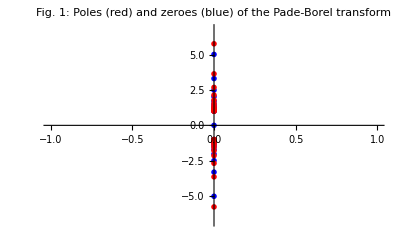

```mathematica
poles = p/.NSolve[Denominator@Together@PBT == 0, p];
zeroes = p/.NSolve[Numerator@PBT == 0, p];

polesPlot = ListPlot[Map[{Re[#], Im[#]}&, poles], PlotStyle->Red,
	PlotMarkers->{Automatic, 0.04}];
zeroesPlot = ListPlot[Map[{Re[#], Im[#]}&, zeroes], PlotStyle->Blue, PlotMarkers->{Automatic, 0.02}];
polesPlotPade = Show[zeroesPlot, polesPlot, PlotLabel->"Fig. 1:\n Poles (red) and zeroes (blue) of the Pade-Borel transform"]
```

### Laplace Transform (Inverse Borel)

```mathematica
<<"SeriesGenerator.wl"
```

Get::noopen: Cannot open SeriesGenerator.wl.

$Failed

```mathematica
xList = Range[0,3+1/2,1/100];
hList = ParallelMap[InverseBorelTransform[PBT, p, (24 #)^(5/4) / 30]&, xList];
yList = - Sqrt[xList / 6] ( 1 + hList ); (* eq. (4) *)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {2.1111988740733698874283832597394964396497770370917×10^223}. NIntegrate obtained 1.6239458184206201186489812702588234016426726756056×10^6 and 1.3635476431947370284639023055040258561880068906875×10^6 for the integral and error estimates.

$Aborted

```mathematica
yPlot = ListPlot[Thread@{xList, yList},
	AxesLabel->{"x", "y(x)"},
	PlotLabel->"Fig. 2",
	PlotLabels -> "ℒ[𝒫ℬ]",
	Joined->True];

tritronquee[x_] := - 0.1875543083 - 0.3049055603 x + 0.1055298557 x^2 - 0.05229396374 x^3;
tritronqueePlot = Plot[tritronquee[x], {x,0,1.8}, PlotStyle->{Gray, Dashed},
	PlotLabels -> "Tritronquee"];
```

```mathematica
Show[yPlot, tritronqueePlot]
```

-Graphics-

### Pole type at p=±i

Using Darboux’s theorem one can find from the large-order growth that it’s a square root branch point.
Following https://epubs.siam.org/doi/10.1137/0139022 :

A function
p(t) = (r(t))/(1 - t/t_1)^-ν + a(t)
r(t) = ∑_(k=0)^∞ b_k(t-t_1)^k analytic in some circle

then p_n ~ (b_0 n^(ν-1))/(t_1^n Gamma[ν])
For some reason I need 2 b_0, I think it’s because there is a conjugate pair of singularities.

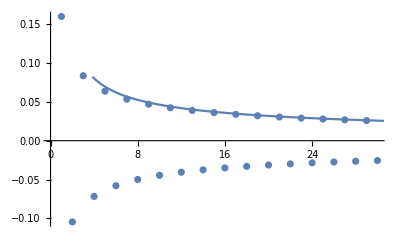

```mathematica
p1 = ListPlot[BTcoeffs];
p2 = Plot[2 * 1/(2 Pi)√(3/5) (n-1)^(1/2-1)/Gamma[1/2], {n,0,50}];
Show[p1,p2]
```

ℬ[h](p) = c/(√(p∓i)),   p→∞

and thus just multiplying ℬ[h](±i) with the square root.

```mathematica
dottedLine = Plot[1 / (2 Pi) Sqrt[3/5], {pp, 0.9, 1}, PlotStyle->{Dashed, Gray},
	PlotLabels->"analytic result"];
singPlotBT = Plot[Re[(Sqrt[p - I] BT) /. p -> I pp], {pp, 0.9, 1.0}, PlotLabels->"Borel"];
singPlotPBT = Plot[Re[(Sqrt[p - I] PBT) /. p -> I pp], {pp, 0.9, 1.0}, PlotStyle->Red,
	PlotLabels->"Pade-Borel"];
Show[dottedLine, singPlotBT, singPlotPBT]
```

-Graphics-

This is not really good, but we can do better

### Conformal Transformation

It turns out to be better to first make a conformal transformation

z = p/(1 + √(1 + p^2))        ⇔    p = (2z)/(1 - z^2)

of the Borel transform, then to expand in a series, make the (analytic continuation) and transform back.

```mathematica
(* Conformal Borel *)
CBT = ConformalMap[BT, p, z];
TCBT = Normal@Series[CBT, {z, 0,2 orderN - 1}]; (* taylor conformal borel *)
PCBT = PadeApproximant[TCBT, {z, 0, {orderN-1, orderN}}];
(*PCBT = Apart[(Numerator@PCBT) / FactorCompletely[Denominator@PCBT, z], z];*)
CPCBT = InverseConformalMap[PCBT, z, p];
```

```mathematica
singPlotPCBT = Plot[Re[(Sqrt[p - I] CPCBT) /. p -> I pp], {pp, 0.9, 1.0}, PlotStyle->Black,
	PlotLabels->"Pade-Conformal-Borel"];
Show[dottedLine, singPlotPBT, singPlotBT, singPlotPCBT, PlotRange->All]
```

-Graphics-

```mathematica
Print["We get for half the Stokes constant at p=i: ", Re[(Sqrt[p - I] CPCBT) /. p -> 0.99999 I // N]];
Print["The correct value is: ", 1 / (2 Pi) Sqrt[3/5] // N];
```

We get for half the Stokes constant at p=i: 0.122936

The correct value is: 0.123281

### Why is conformal so much better?

```mathematica
polesPlotPade
```

-Graphics-

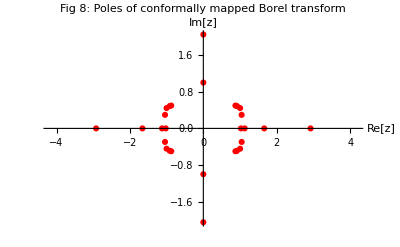

```mathematica
polesC = z/.NSolve[Denominator@Together@PCBT == 0, z];
polesPlotC = ListPlot[Map[{Re[#], Im[#]}&, polesC], PlotStyle->Red,
	AxesLabel->{"Re[z]", "Im[z]"},
	PlotMarkers->{Automatic, 0,04},
	PlotLabel->"Fig 8:\n Poles of conformally mapped Borel transform"]
```

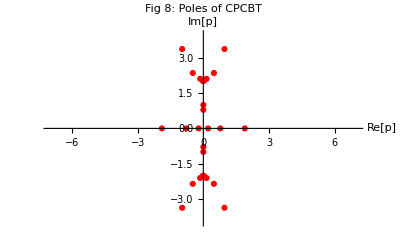

```mathematica
(* z plane poles (conformal) mapped back to Borel plane p *)
polesCPCBT = (2 # / (1 - #^2)&) @ polesC;
polesPlotCPCBT = ListPlot[Map[{Re[#], Im[#]}&, polesCPCBT], PlotStyle->Red,
	AxesLabel->{"Re[p]", "Im[p]"},
	PlotLabel->"Fig 8:\n Poles of CPCBT",
	PlotMarkers->{Automatic, 0,04},
	PlotRange->{{-7,7}, {-4,4}}]
```

### Inverse Borel of Conformal

```mathematica
hListC = ParallelMap[InverseBorelTransform[CPCBT, p, (24 #)^(5/4) / 30]&, xList];
yListC = - Sqrt[xList / 6] ( 1 + hListC ); (* eq. (4) *)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {2.1111988740733698874283832597394964396497770370917×10^223}. NIntegrate obtained 9.8700166679002836179265430555966486323246031187172×10^252580 and 9.8700166679002836179265430555966486323246031187172×10^252580 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {568.40519410849960659223405466349701409939166249152}. NIntegrate obtained 1.4463637977110638929824851974373006939274563869137 and 2.0091354114514964474695341025657627799140241282923×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {143.48161299340554078333679339934346501279718217886}. NIntegrate obtained 0.53208788111548485654968900448942690832987765951096 and 2.3714474878496174025996654483994510009973921059763×10^-30 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
yPlotC = ListPlot[Thread@{xList, yListC},
	AxesLabel->{"x", "y(x)"},
	Joined->True,
	PlotStyle->Red,
	PlotRange->{{0,0.3},{-0.8,0}},
	PlotLabels->"Pade-Comformal-Borel"];
```

```mathematica
Show[yPlot, tritronqueePlot]
```

-Graphics-

```mathematica
Show[yPlot, tritronqueePlot, yPlotC, PlotRange->{{0,0.3}, {-0.17,-0.27}}, Frame->True]
```

-Graphics-

## Reexpansion Closer to Origin

## Explanation

```mathematica
PIDEQ = y''[x] == 6 y[x]^2 - x
```

y''[x]==-x+6 y[x]^2

```mathematica
D[PIDEQ, x]
```

y^(3)[x]==-1+12 y[x] y'[x]

```mathematica
dyn[x_, n_/;n>1] := D[PIDEQ, {x,n-2}][[2]]
```

```mathematica
dyn[x,2]
```

-x+6 y[x]^2

```mathematica
dyn[x,3]
```

-1+12 y[x] y'[x]

```mathematica
dyn[x,4]
```

6 (2 y'[x]^2+2 y[x] y''[x])

## Implementation

### Reexpansion of Pade-Borel

```mathematica
Get@FileNameJoin[{NotebookDirectory[], "source", "SeriesGenerator.wl"}]
```

```mathematica
orderN = 50;
oderReexp = 2 orderN ; (* initial expansion was in 1/t^2, new expansion in 1/x *)
coeffs = Painleve1PertSol[orderN];
```

```mathematica
BT = BorelTransform[coeffs, p];
PBT = PadeApproximant[BT, {p, 0, {orderN-1, orderN}}];
(*PBT = Apart[(Numerator@PBT) / FactorCompletely[Denominator@PBT, p], p];*)
```

```mathematica
yy[x_, h_] = - Sqrt[(x/6)] ( 1 + h[t[x]] );
tt[x_] = (24 x)^(5/4)/30;
dy[x_, h_, dh_] = D[yy[x, h], x] /. {h[t_]->h, h'[t_]->dh, t -> tt};
ddy[x_, h_, dh_, ddh_] = D[yy[x, h], x,x] /. {h[t_]->h, h'[t_]->dh, h''[t_]->ddh, t -> tt};
```

We want to reexpand around x0=3, so we calculate y[3] and y’[3]

```mathematica
x0 = 3;
h0 = InverseBorelTransform[PBT, p, (24 x0)^(5/4) / 30,
	PrecisionGoal -> 50, WorkingPrecision -> 100];
dh0 = InverseBorelTransform[(-p)PBT, p, (24 x0)^(5/4) / 30,
	PrecisionGoal -> 50, WorkingPrecision -> 100];
ddh0 = InverseBorelTransform[(-p)^2PBT, p, (24 x0)^(5/4) / 30,
	PrecisionGoal -> 50, WorkingPrecision -> 100];
y0 = yy[x,h]/.{h[t_]->h} /. {x->x0, h->h0};
dy0 = dy[x0, h0, dh0];
(* ddy0 = ddy[x0, h0, dh0, ddh0]; *) (* for testing *)
```

```mathematica
yReexpanded[x_] = ReexpandP1[{y0, dy0}, {x, x0}, oderReexp];
yReexpandedPade[x_] = PadeApproximant[yReexpanded[x], {x, x0, {oderReexp/2-1, oderReexp/2}}];
(*yReexpandedPade[x_] = Apart[(Numerator@yReexpandedPade[x]) / FactorCompletely[Denominator@yReexpandedPade[x], x], x];*)
```

```mathematica
tritronquee[x_] := - 0.1875543083 - 0.3049055603 x + 0.1055298557 x^2 - 0.05229396374 x^3;
tritronqueePlot = Plot[tritronquee[x], {x,0,3.5}, PlotStyle->{Gray, Dashed}];
```

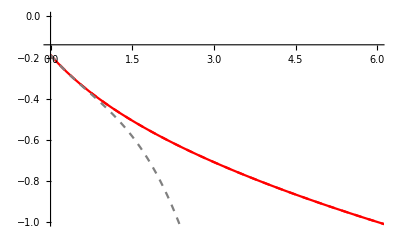

```mathematica
yReexpPlot = Plot[Re@yReexpanded[x], {x,0,7}, PlotStyle->{Dashed, Red}];
yReexpPadePlot = Plot[Re@yReexpandedPade[x], {x,0,7}, PlotStyle->Red];
yPlot = ListPlot[Thread@{xList, yList}, Joined->True, PlotStyle->{Blue, Dashed}];
Show[yReexpPlot, yReexpPadePlot, yPlot, tritronqueePlot, PlotRange->{{0,6}, {-1,0}}]
```

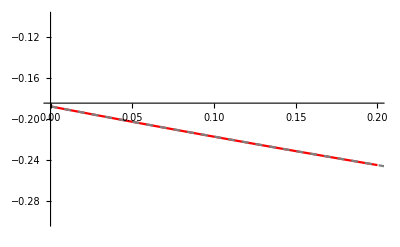

```mathematica
yReexpPlot = Plot[Re@yReexpanded[x], {x,0,0.2}, PlotStyle->{Dashed, Red}];
yReexpPadePlot = Plot[Re@yReexpandedPade[x], {x,0,0.2}, PlotStyle->Red];
yPlot = ListPlot[Thread@{xList, yList}, Joined->True, PlotStyle->{Blue, Dashed}];
Show[yReexpPadePlot, yPlot, tritronqueePlot, PlotRange->{{0,0.2},{-0.3, -0.1}}]
```

yReexpPade is pretty much spot on with Tritronquee!

```mathematica
yReexpanded[0]
```

-0.1875543083404948938386730547251110034708554725007493606951234126290820433030155955583059477270468

```mathematica
yReexpandedPade[0]
```

-0.1875543083404948938386728761870094087733260766072482195194863342192957951645418782020051

From the paper: −0.187554308340

### Pade-Conformal-Borel

```mathematica
CBT = ConformalMap[BT, p, z];
TCBT = Normal@Chop@Series[CBT, {z, 0,2 orderN - 1 }]; (* taylor conformal borel *)
PCBT = PadeApproximant[TCBT, {z, 0, {orderN-1, orderN}}];
PCBT = Apart[(Numerator@PCBT) / FactorCompletely[Denominator@PCBT, z], z];
CPCBT = InverseConformalMap[PCBT, z, p];
```

```mathematica
x0 = 3;
h0C = InverseBorelTransform[CPCBT, p, (24 x0)^(5/4) / 30,
	PrecisionGoal -> 50, WorkingPrecision -> 100];
dh0C = InverseBorelTransform[(-p)CPCBT, p, (24 x0)^(5/4) / 30,
	PrecisionGoal -> 50, WorkingPrecision -> 100];
ddh0C = InverseBorelTransform[(-p)^2 CPCBT, p, (24 x0)^(5/4) / 30,
	PrecisionGoal -> 50, WorkingPrecision -> 100];
y0C = yy[x,h]/.{h[t_]->h} /. {x->x0, h->h0C};
dy0C = dy[x0, h0C, dh0C];
```

```mathematica
yReexpandedC[x_] = ReexpandP1[{y0C, dy0C}, {x, x0}, oderReexp];
yReexpandedPadeC[x_] = PadeApproximant[yReexpandedC[x], {x, x0, {oderReexp/2-1,oderReexp/2}}];
yReexpandedPadeCApart[x_] = Chop@Apart[(Numerator@yReexpandedPadeC[x]) / FactorCompletely[Denominator@yReexpandedPadeC[x], x], x];
```

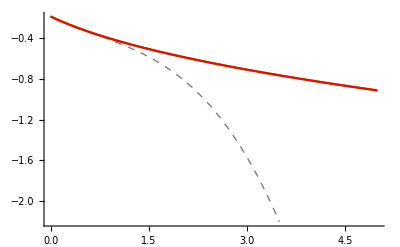

```mathematica
yReexpPlot = Plot[yReexpanded[x], {x,0,2}, PlotStyle->{Dashed, Red}];
yReexpPadePlot = Plot[Re@yReexpandedPade[x], {x,0,5}, PlotStyle->Red];
yReexpPadeCPlot = Plot[Re@yReexpandedPadeC[x], {x,0,5}, PlotStyle->{Green}];
yPlot = ListPlot[Thread@{xList, Re@yList}, Joined->True, PlotStyle->{Blue, Dashed}];
tritronquee[x_] := - 0.1875543083 - 0.3049055603 x + 0.1055298557 x^2 - 0.05229396374 x^3;
tritronqueePlot = Plot[tritronquee[x], {x,0,3.5}, PlotStyle->{Gray, Dashed, Thick}];

Show[yReexpPadeCPlot, yReexpPadePlot, tritronqueePlot, PlotRange->{{0,0.6}, {-0.35, -0.17}}];
Show[tritronqueePlot, yReexpPadeCPlot, yReexpPadePlot,yPlot, PlotRange->Automatic]
```

```mathematica
yReexpandedPadeC[0]
```

-0.1875543083404948938386817575958329932311609097621389969333726946492002853764167283263747

## Going to negative x

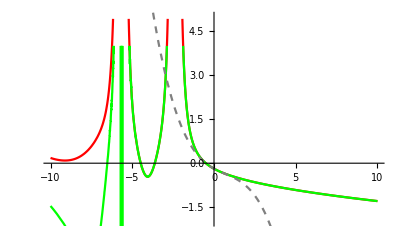

```mathematica
yReexpPlot = Plot[Re@yReexpanded[x], {x,-10, 10}, PlotStyle->{Dashed, Red}];
yReexpPadePlot = Plot[Re@yReexpandedPade[x], {x,-10, 10}, PlotStyle->Red];
yReexpPadeCPlot = Plot[Re@yReexpandedPadeC[x], {x,-10, 10}, PlotStyle->{Green}];
yPlot = ListPlot[Thread@{xList, yList}, Joined->True, PlotStyle->{Blue, Dashed}];
tritronquee[x_] := - 0.1875543083 - 0.3049055603 x + 0.1055298557 x^2 - 0.05229396374 x^3;
tritronqueePlot = Plot[tritronquee[x], {x,-10, 10}, PlotStyle->{Gray, Dashed}];

Show[yReexpPadePlot, yReexpPadeCPlot, yReexpPlot, tritronqueePlot, PlotRange->{{-10, 10}, {-2,5}}]
```

For more terms we can get more than the first pole correct.

```mathematica
poles = x/.Solve[Denominator@yReexpandedPadeC[x] == 0, x];
```

```mathematica
(*poles = x/. Solve[1/yReexpandedPade[x]==0, x]*)
```

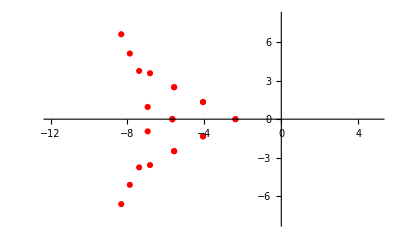

```mathematica
polesPlot = ListPlot[Map[{Re[#], Im[#]}&, poles], PlotStyle->Red, PlotRange->{{-12, 5}, {-8, 8}}]
```

## Connection Formulas

### Formula 1

```mathematica
connectionFormula1[x_] := Exp[(- 3 Pi I)/4]/(2^(5/4) 6^(1/8)√Pi) Exp[- I (24 x)^(5/4)/30]/x^(1/8);
```

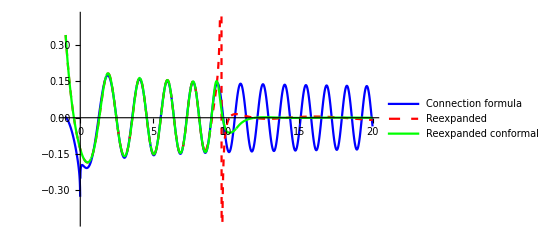

```mathematica
Plot[{Re@connectionFormula1[x], 
	Re[yReexpandedPade[x] - Exp[8 Pi I / 5] yReexpandedPade[Exp[4 Pi I / 5] x]],
	Re[yReexpandedPadeC[x] - Exp[8 Pi I / 5] yReexpandedPadeC[Exp[4 Pi I / 5] x]]}
	, {x,-1, 20}, 
	PlotStyle->{Blue, {Red, Dashed}, Green},
	PlotLegends->{"Connection formula", "Reexpanded", "Reexpanded conformal"}]
```

### Formula 2

```mathematica
connectionFormula2[x_] := Exp[- (3 Pi I)/4 + (I Pi)/20]/(2^(5/4) 6^(1/8)√Pi)Exp[- (24 x)^(5/4)/30]/x^(1/8);
```

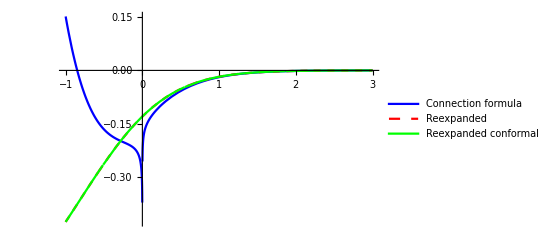

```mathematica
Plot[{Re@connectionFormula2[x], 
	Re[yReexpandedPade[Exp[- 2 Pi I / 5] x] - Exp[8 Pi I / 5] yReexpandedPade[Exp[2 Pi I / 5] x]],
	Re[yReexpandedPadeC[Exp[- 2 Pi I / 5]x] - Exp[8 Pi I / 5] yReexpandedPadeC[Exp[2 Pi I / 5] x]]}
	, {x,-1, 3}, 
	PlotStyle->{Blue, {Red, Dashed}, Green},
	PlotLegends->{"Connection formula", "Reexpanded", "Reexpanded conformal"}]
```